# V_eff calculation

## Effective Potential

### Interpolate the thermal integral functions

```mathematica
JB[x_]:=NIntegrate[z^2*Log[1-Exp[-Sqrt[z^2+x]]],{z,0,Infinity}]
(*bosonic field contributions*)
JF[x_]:=NIntegrate[z^2*Log[1+Exp[-Sqrt[z^2+x]]],{z,0,Infinity}]
(*fermionic field contributions*)
(*Cross check*)
fit11=Table[{ϕ,JB[ϕ]},{ϕ,10^(-1),200,.1}];
JBfit11[ϕ_]=Fit[fit11,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit12=Table[{ϕ,JB[ϕ]},{ϕ,10^(-3),10^(-1),10^(-3)}];
JBfit12[ϕ_]=Fit[fit12,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit13=Table[{ϕ,JB[ϕ]},{ϕ,0,10^(-3),10^(-6)}];
JBfit13[ϕ_]=Fit[fit13,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit21=Table[{ϕ,JF[ϕ]},{ϕ,10^(-1),200,.1}];
JFfit21[ϕ_]=Fit[fit21,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit22=Table[{ϕ,JF[ϕ]},{ϕ,10^(-3),10^(-1),10^(-3)}];
JFfit22[ϕ_]=Fit[fit22,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit23=Table[{ϕ,JF[ϕ]},{ϕ,0,10^(-3),10^(-6)}];
JFfit23[ϕ_]=Fit[fit23,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
JBfit[x_]:=JBfit11[x]/;10^(-1)<x≤200
JBfit[x_]:=JBfit12[x]/;10^(-3)<=x≤10^(-1)
JBfit[x_]:=JBfit13[x]/;0<=x≤10^(-3)
JBfit[x_]:=0/;200<x
JFfit[x_]:=JFfit21[x]/;10^(-1)<x≤200
JFfit[x_]:=JFfit22[x]/;10^(-3)<=x≤10^(-1)
JFfit[x_]:=JFfit23[x]/;0<=x≤10^(-3)
JFfit[x_]:=0/;200<x;
```

### Effective Potential

```mathematica
Clear[B,DD,EE,T0]
```

```mathematica
vR=15000;
g=0.65;
gX=√(0.36^2 g^2/(g^2-0.36^2));
yt=0.76;
yE=0.6;
mt[ϕ_]:=yt^2 ϕ^2/2;
mE[ϕ_]:=yE^2 ϕ^2/2
mW[ϕ_]:=g^2 ϕ^2/4;
mZ[ϕ_]:=(g^2+gX^2)ϕ^2/4;
mH[λ_,ϕ_]:=3λ ϕ^2-λ vR^2;(*Physical Subscript[h, R]*)
mX[λ_,ϕ_]:=λ ϕ^2-λ vR^2;(*Goldstone bosons*)
mgauge=({{g^2 x1^2/4+11/6 g^2 x2^2, -g gX x1^2/4}, {-g gX x1^2/4, gX^2 x1^2/4+29/18 g^2 x2^2}});
(*x1 is the field. x2 is the temperature. This is the mixing between W3 and Subscript[B, X]*)
gaugeL=Eigenvalues[mgauge]//FullSimplify;
B[λ_]:=1/(64 π^2 vR^4)(6 mW[vR]^2+3 mZ[vR]^2+mH[λ,vR]^2-12 mt[vR]^2-8 mE[vR]^2);
mWL[ϕ_,T_]:=1/4 g^2 ϕ^2+11/6 g^2 T^2;(*longitudal mode for W+ and W-, or W1 and W2*)
mBL[ϕ_,T_]:=gaugeL[[1]]/.{x1->ϕ,x2->T};(*SM B particle, massless*)
mZL[ϕ_,T_]:=gaugeL[[2]]/.{x1->ϕ,x2->T};(*Zprime particle*)
mHT[λ_,ϕ_,T_]:=3λ ϕ^2-λ vR^2+1/2 λ T^2+1/4*yt^2 T^2+1/8 g^2 T^2+1/16(g^2+gX^2)T^2;
mXT[λ_,ϕ_,T_]:=λ ϕ^2-λ vR^2+1/2 λ T^2+1/4*yt^2 T^2+1/8 g^2 T^2+1/16(g^2+gX^2)T^2;
V0[λ_,ϕ_]:=-1/2 λ vR^2 ϕ^2+λ/4 ϕ^4;
VCW[λ_,ϕ_,T_]:=1/(64 π^2)(4 mW[ϕ]^2(Log[mW[ϕ]/vR^2]-1/2)+2 mWL[ϕ,T]^2(Log[mWL[ϕ,T]/vR^2]-3/2)+2 mZ[ϕ]^2(Log[mZ[ϕ]/vR^2]-1/2)+mZL[ϕ,T]^2(Log[mZL[ϕ,T]/vR^2]-3/2)+mBL[ϕ,T]^2(Log[mBL[ϕ,T]/vR^2]-3/2)+mHT[λ,ϕ,T]^2(Log[Abs[mHT[λ,ϕ,T]]/vR^2]-3/2)+3 mXT[λ,ϕ,T]^2(Log[Abs[mXT[λ,ϕ,T]]/vR^2]-3/2)-12 mt[ϕ]^2(Log[mt[ϕ]/vR^2]-1/2)-8 mE[ϕ]^2(Log[mE[ϕ]/vR^2]-1/2));
(*Coleman-Weinberg potential, with Parwani resummation*)
VCWnore[λ_,ϕ_]:=1/(64 π^2)(4 mW[ϕ]^2(Log[mW[ϕ]/vR^2]-1/2)+2 mW[ϕ]^2(Log[mW[ϕ]/vR^2]-3/2)+2 mZ[ϕ]^2(Log[mZ[ϕ]/vR^2]-1/2)+mZ[ϕ]^2(Log[mZ[ϕ]/vR^2]-3/2)+mH[λ,ϕ]^2(Log[Abs[mH[λ,ϕ]]/vR^2]-3/2)+3 mX[λ,ϕ]^2(Log[Abs[mX[λ,ϕ]]/vR^2]-3/2)-12 mt[ϕ]^2(Log[mt[ϕ]/vR^2]-1/2)-8 mE[ϕ]^2(Log[mE[ϕ]/vR^2]-1/2));
VB[λ_,ϕ_]:=2B[λ] vR^2 ϕ^2-3/2 B[λ] ϕ^4+B[λ] ϕ^4 Log[ϕ^2/vR^2];
VFT[λ_,ϕ_,T_]:=T^4/(2 π^2)(4JBfit[mW[ϕ]/T^2]+2JBfit[mWL[ϕ,T]/T^2]+2JBfit[mZ[ϕ]/T^2]+JBfit[mZL[ϕ,T]/T^2]+JBfit[mBL[ϕ,T]/T^2]+JBfit[Abs[mHT[λ,ϕ,T]]/T^2]+3JBfit[Abs[mXT[λ,ϕ,T]]/T^2]-12JFfit[mt[ϕ]/T^2]-8JFfit[mE[ϕ]/T^2]);
VFTnore[λ_,ϕ_,T_]:=T^4/(2 π^2)(6JBfit[mW[ϕ]/T^2]+3JBfit[mZ[ϕ]/T^2]+JBfit[Abs[mH[λ,ϕ]]/T^2]+3JBfit[Abs[mX[λ,ϕ]]/T^2]-12JFfit[mt[ϕ]/T^2]-8JFfit[mE[ϕ]/T^2]);
VCWtot[λ_,ϕ_,T_]:=V0[λ,ϕ]+VCW[λ,ϕ,T]+VFT[λ,ϕ,T]-(V0[λ,10^-3]+VCW[λ,10^-3,T]+VFT[λ,10^-3,T]);
Vring[λ_,ϕ_,T_]:=T/(12π)(2(mW[ϕ]^(3/2)-mWL[ϕ,T]^(3/2))+(mZ[ϕ]^(3/2)-mZL[ϕ,T]^(3/2))-mBL[ϕ,T]^(3/2)+(Abs[mH[λ,ϕ]]^(3/2)-Abs[mHT[λ,ϕ,T]]^(3/2))+3(Abs[mX[λ,ϕ]]^(3/2)-Abs[mXT[λ,ϕ,T]]^(3/2)))
VBtot[λ_,ϕ_,T_]:=V0[λ,ϕ]+VB[λ,ϕ]+VFT[λ,ϕ,T]-(V0[λ,10^-3]+VB[λ,10^-3]+VFT[λ,10^-3,T]);
VBArnold[λ_,ϕ_,T_]:=V0[λ,ϕ]+VB[λ,ϕ]+VFTnore[λ,ϕ,T]+Vring[λ,ϕ,T]-(V0[λ,10^-3]+VB[λ,10^-3]+VFTnore[λ,10^-3,T]+Vring[λ,10^-3,T]);
VCWArnold[λ_,ϕ_,T_]:=V0[λ,ϕ]+VCWnore[λ,ϕ]+VFTnore[λ,ϕ,T]+Vring[λ,ϕ,T]-(V0[λ,10^-3]+VCWnore[λ,10^-3]+VFTnore[λ,10^-3,T]+Vring[λ,10^-3,T]);
VBnoresum[λ_,ϕ_,T_]=V0[λ,ϕ]+VB[λ,ϕ]+VFTnore[λ,ϕ,T]-(V0[λ,10^-3]+VB[λ,10^-3]+VFTnore[λ,10^-3,T]);
DD[λ_]:=1/(24 vR^2)(6mW[vR]+3mZ[vR]+mH[λ,vR]+6mt[vR]+4mE[vR]);
EE[λ_]:=1/(12π vR^3)(6 mW[vR]^(3/2)+3 mZ[vR]^(3/2)+mH[λ,vR]^(3/2));
T0[λ_]:=(√(mH[λ,vR]-8 B[λ] vR^2))/(√(4 DD[λ]))
VhighT[λ_,ϕ_,T_]:=DD [λ](T^2-T0[λ]^2)ϕ^2-EE[λ] T ϕ^3+1/4 λ ϕ^4;
```

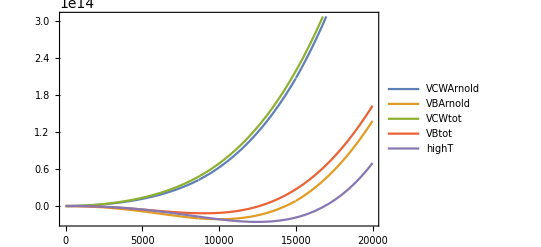

```mathematica
Plot[{VCWArnold[0.01,ϕ,3500],VBArnold[0.01,ϕ,3500],VCWtot[0.01,ϕ,3500],VBtot[0.01,ϕ,3500],VhighT[0.01,ϕ,3500]},{ϕ,0,20000},PlotLegends->{"VCWArnold","VBArnold","VCWtot","VBtot","highT"}]
```

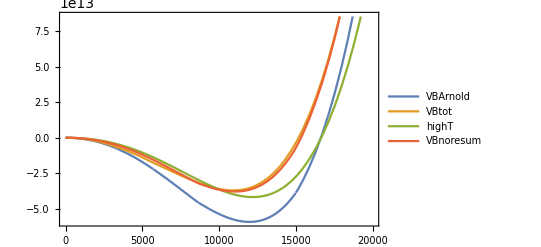

```mathematica
Plot[{VBArnold[0.015,ϕ,4400],VBtot[0.015,ϕ,4400],VhighT[0.015,ϕ,4400],VBnoresum[0.015,ϕ,4400]},{ϕ,0,20000},PlotLegends->{"VBArnold","VBtot","highT","VBnoresum"}]
```

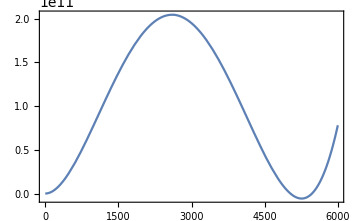

```mathematica
Plot[{VBnoresum[0.015,ϕ,4587.5]},{ϕ,0,6000}]
```

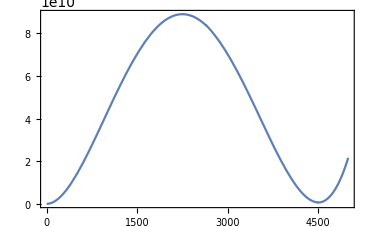

```mathematica
Plot[VBArnold[0.013,ϕ,4619.],{ϕ,0,5000}]
```

## Calculate the wall profile

```mathematica
SetDirectory[NotebookDirectory[]]
<<anybubble.m
<<powell.m
Options[FindBubble]
```

/Users/isaac/Dropbox/Project/2021-9-local_EWBG_parity/phase transition

{Verbose→False,SpaceTimeDimension→3,StartAnalyticFraction→1/100,EndAnalyticFraction→1/100,MaxIntervalGrowth→30,MaxReadjustments→20,InitialProfilePoints→{},PowellVerbosity→1,MaxIterations→500,AccuracyGoal→Automatic,WorkingPrecision→MachinePrecision}

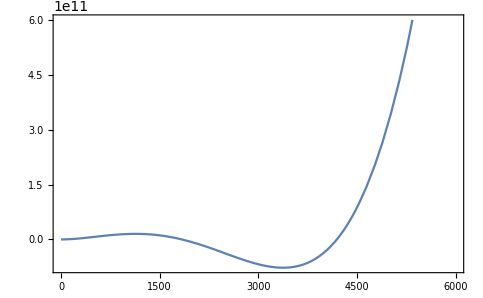

```mathematica
Plot[VBArnold[0.015,ϕ,4968.8],{ϕ,0,6000}]
```

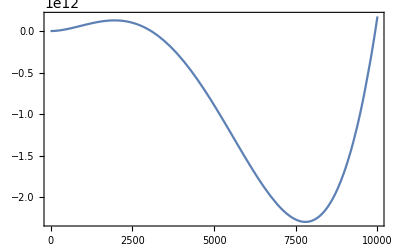

```mathematica
Plot[VhighT[0.015,ϕ,4720],{ϕ,0,10000}]
```

### Find the nucleation temperature λ=0.015

```mathematica
T1=4968.8;
fitting=Table[{ϕ,VBArnold[0.015,ϕ,T1]},{ϕ,1,6000,10}];
Vfit[ϕ_]=Fit[fitting,{1,ϕ,ϕ^2,ϕ^3,ϕ^4,ϕ^5,ϕ^6,ϕ^7,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
xr=x/.Minimize[{Vfit[x]-Vfit[0],{1000<x<6000}},x][[2]];
SbyT=(FindBubble[Vfit[x[1]]-Vfit[0],x,{xr},{0}]/T1)[[1]]
```

...................

129.824

..........................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................

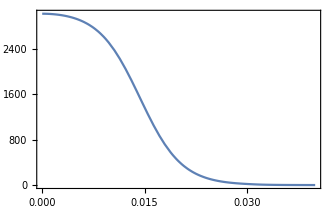

```mathematica
Plot[FindBubble[Vfit[x[1]]-Vfit[0],x,{xr},{0}][[2]][r],{r,0,0.04}]
```

Wall thickness 84.2/T.

```mathematica
α=0.65^2/(4π);
1/α
```

29.7429

## Baryon asymmetry

```mathematica
Tn=2/3 vR;
s=2 π^2/45*100*Tn^3;
σ=3;
αR=g^2/(4π);
M=2vR;
Γsph=20*αR^5 Tn^4;
ratio=28/79*1/s(4Γsph σ^2 αR^2 Tn)/(M^2 g^2)
```

7.4301×10^-11

```mathematica
50^2/(2*246^2)//N
```

0.0206557